```mathematica
Needs["PlotLegends`"]
```

```mathematica
trDistUnenc[α_,wt_]:=√(1-ⅇ^(-4 wt α^2));
trDistEnc[α_,wt_,m_,d_]:=∑_(k=1)^d ⅇ^(-m α^2)((m α^2)^k)/(k!)√(1-((m-2 wt)/m)^(2k));
```

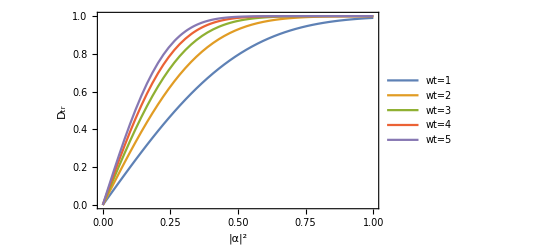

```mathematica
figUnenc=Plot[{trDistUnenc[α,1],trDistUnenc[α,2],trDistUnenc[α,3],trDistUnenc[α,4],trDistUnenc[α,5]},{α,0,1},Frame->True,FrameLabel->{"|α|^2","D_tr"},LabelStyle->{FontSize->15},PlotLegends->{"wt=1","wt=2","wt=3","wt=4","wt=5"},PlotRange->{0,1}];
Show[figUnenc]
```

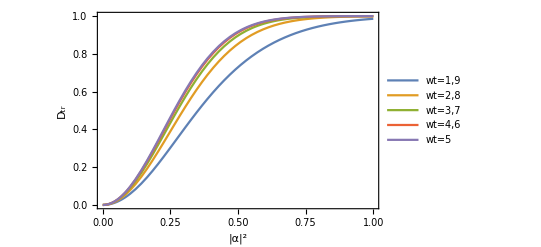

```mathematica
thisD=50;
thisM=10;
figEnc=Plot[{trDistEnc[α,1,thisM,thisD],trDistEnc[α,2,thisM,thisD],trDistEnc[α,3,thisM,thisD],trDistEnc[α,4,thisM,thisD],trDistEnc[α,5,thisM,thisD]},{α,0,1},Frame->True,FrameLabel->{"|α|^2","D_tr"},LabelStyle->{FontSize->15},PlotLegends->{"wt=1,9","wt=2,8","wt=3,7","wt=4,6","wt=5"},PlotRange->{0,1}];
Show[figEnc]
```

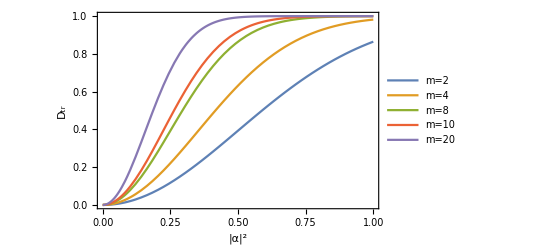

```mathematica
thisD=50;
thisM=10;
Plot[{trDistEnc[α,1,2,thisD],trDistEnc[α,2,4,thisD],trDistEnc[α,4,8,thisD],trDistEnc[α,5,10,thisD],trDistEnc[α,10,20,thisD]},{α,0,1},Frame->True,FrameLabel->{"|α|^2","D_tr"},LabelStyle->{FontSize->15},PlotLegends->{"m=2","m=4","m=8","m=10","m=20"},PlotRange->{0,1}]
```

{{1.,0.},{2.,0.393469},{3.,0.506526},{4.,0.632121},{5.,0.706077},{6.,0.776869},{7.,0.823048},{8.,0.864656},{9.,0.893088},{10.,0.917853}}

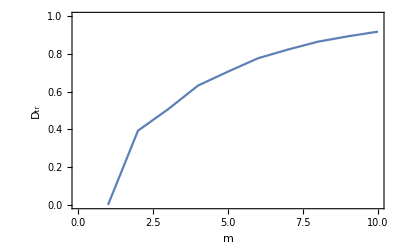

```mathematica
thisD=10;
thisAlpha=0.5;
data=N[Table[{thisM,trDistEnc[thisAlpha,Floor[thisM/2],thisM,thisD]},{thisM,1,10}]]
ListLinePlot[data,Frame->True,FrameLabel->{"m","D_tr"},LabelStyle->{FontSize->15},PlotRange->{0,1}]
```